```mathematica
dataDir=FileNameJoin[{DirectoryName[NotebookDirectory[]]}]<>"\\outputs\\";
```

## target tracking

### data prep

```mathematica
Map[
Module[
{filtered},
filtered=Import[#<>"\\11\\data.txt","CSV"][[All,{2,-4,-3,-2,-1}]];
Export[#<>"\\tracking.txt",filtered,"CSV"];
]
&,FileNames[All,dataDir<>ToString[series]<>"\\"]
];
```

## statistical learning

### data

```mathematica
series=1;
```

```mathematica
subjectResponses=Map[
Flatten[Import[#<>"\\12\\subject_responses.csv"]]
&,FileNames[All,dataDir<>ToString[series]<>"\\"]
];
```

### percent correct

```mathematica
GetMeanAndSEM[Map[Mean,subjectResponses]]//N
```

{0.52963,0.0291294}

```mathematica
Transpose[{
1+0.25Range[Length[subjectResponses]]/Length[subjectResponses],
Map[Mean,subjectResponses]
}]
```

{{1.01667,7/18},{1.03333,5/9},{1.05,11/18},{1.06667,11/18},{1.08333,17/36},{1.1,1/2},{1.11667,7/12},{1.13333,5/12},{1.15,7/12},{1.16667,19/36},{1.18333,25/36},{1.2,13/36},{1.21667,5/9},{1.23333,13/36},{1.25,13/18}}

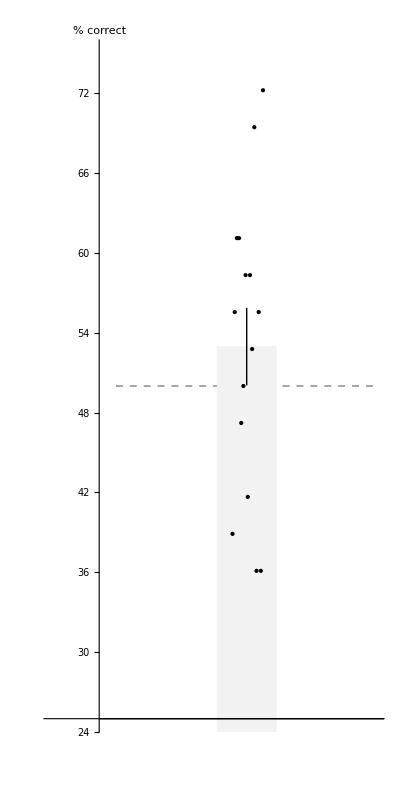

```mathematica
BarChart[
{100Mean[Map[Mean,subjectResponses]]},
PlotRange->{{-2,3},{25,75}},AspectRatio->2,ChartStyle->GrayLevel[0.95],AxesLabel->{None,"% correct"},
Prolog->{
Gray,Dashed,Line[{{-1,50},{3,50}}]
},
Epilog->{
Map[
Point,
Transpose[{
(1-0.5/2)+0.5Range[Length[subjectResponses]]/Length[subjectResponses],
100Map[Mean,subjectResponses]
}]
],
Thick,
Line[{
{1,100Mean[Map[Mean,subjectResponses]]-100StandardError[Map[Mean,subjectResponses]]},
{1,100Mean[Map[Mean,subjectResponses]]+100StandardError[Map[Mean,subjectResponses]]}
}]
}
]
```